```mathematica
sol=DSolve[{y''[x]-2y'[x]+y[x]==0, y[0]==3, y'[0]==1},y,x]
sol1=DSolve[{y''[x]-2y'[x]+y[x]==0, y[0]==3, y'[0]==0},y,x]
sol2=DSolve[{y''[x]-2y'[x]+y[x]==0, y[0]==3, y'[0]==-6},y,x]
sol3=DSolve[{y''[x]-2y'[x]+y[x]==0, y[0]==3, y'[0]==-1},y,x]
sol4=DSolve[{y''[x]-2y'[x]+y[x]==0, y[0]==3, y'[0]==6},y,x]
sol5=DSolve[{y''[x]-2y'[x]+y[x]==0, y[0]==3, y'[0]==3},y,x]
```

{{y→Function[{x},-ⅇ^x (-3+2 x)]}}

{{y→Function[{x},-3 ⅇ^x (-1+x)]}}

{{y→Function[{x},-3 ⅇ^x (-1+3 x)]}}

{{y→Function[{x},-ⅇ^x (-3+4 x)]}}

{{y→Function[{x},3 ⅇ^x (1+x)]}}

{{y→Function[{x},3 ⅇ^x]}}

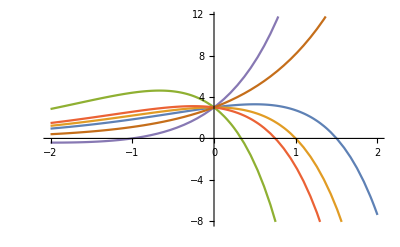

```mathematica
Plot[{ -ⅇ^x (-3+2 x), -3 ⅇ^x (-1+x),-3 ⅇ^x (-1+3 x),  -ⅇ^x (-3+4 x),3 ⅇ^x (1+x), 3 ⅇ^x  }, {x,-2,2}, BaseStyle->{FontSize->14, FontWeight->Bold}]
```

```mathematica
p1=Plot[Evaluate[y[x]/.sol], {x,-2,2}]
p2=Plot[Evaluate[y[x]/.sol1], {x,-2,2}]
p3=Plot[Evaluate[y[x]/.sol2], {x,-2,2}]
p4=Plot[Evaluate[y[x]/.sol3], {x,-2,2}]
p5=Plot[Evaluate[y[x]/.sol4], {x,-2,2}]
p6=Plot[Evaluate[y[x]/.sol5], {x,-2,2}]
Show[{p1, p2 , p3,p4, p5, p6}  , {x,-2,2},PlotRange->Automatic]
```

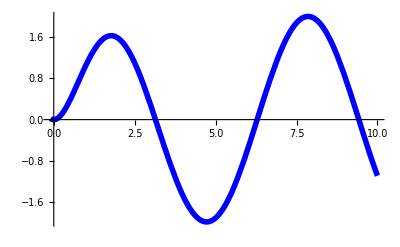

```mathematica
sol=DSolve[{y''[x]+ 2y'[x]+ 2y[x]==4Cos[x] + 2Sin[x], y[0]==0, y'[0]==0},y,x];
Plot[Evaluate[y[x]/.sol], {x,-.1,10},
 BaseStyle->{FontSize->14, FontWeight->Bold},
PlotStyle->{Blue, Thickness[.01] }]
```

```mathematica
sol=DSolve[ {y''[x]-4y[x]==(x^2 - 3) *Sin[2x]},y,x]
```

{{y→Function[{x},ⅇ^(2 x) C[1]+ⅇ^(-2 x) C[2]+1/32 (-4 x Cos[2 x]+13 Sin[2 x]-4 x^2 Sin[2 x])]}}

```mathematica
Plot[{ (-2) }, {x,-2,2}, BaseStyle->{FontSize->14, FontWeight->Bold}]
```

```mathematica
DSolve[{x'[t]==5x[t] + 3y[t] - 2 ⅇ^-t + 1 ,y'[t]==-x[t] + y[t] + ⅇ^-t -5t+ 7, x[0]==0, y[0]==0},{y[t],x[t]},t]
```

{{x[t]→1/480 ⅇ^-t (224+525 ⅇ^t-1820 ⅇ^(3 t)+1071 ⅇ^(5 t)-900 ⅇ^t t),y[t]→-1/480 ⅇ^-t (128+1335 ⅇ^t-1820 ⅇ^(3 t)+357 ⅇ^(5 t)-1500 ⅇ^t t)}}